Вариант 5

Задание 1

```mathematica
f[x_]=5(Tan[x])^2+Cos[x];
X={0,Pi/6,Pi/4,Pi/3,Pi/12,Pi,9*Pi/5}; xx=Pi/8;
F=f[X];
Subscript[x, k_]:=X[[k+1]];
Subscript[f, k_]:=F[[k+1]];
NN=Length[X];
n=(NN-1)/2;
koef=Solve[Table[Subscript[a, 0]+∑_(k=1)^n (Subscript[a, k] Sin[k*Subscript[x, j]]+Subscript[b, k] Cos[k*Subscript[x, j]])==Subscript[f, j],{j,0,NN-1}],{}]//Flatten;
T[x_]=Subscript[a, 0]+∑_(k=1)^n (Subscript[a, k] Sin[k*x]+Subscript[b, k] Cos[k*x])/.koef//FullSimplify
Table[(T[Subscript[x, j]]//N)==(Subscript[f, j]//N),{j,0,NN-1}]
Gr1=ListPlot[MapThread[List,{X,F}],PlotStyle->{PointSize[0.02]}];
Gr2=Plot[f[y],{y,Subscript[x, 0],Subscript[x, NN-1]}];
Gr3=Plot[T[y],{y,Subscript[x, 0],Subscript[x, NN-1]},PlotStyle->Red];
Show[Gr1,Gr2,Gr3]
T[xx]//N
Abs[f[xx]-T[xx]]
```

Задание 2

5 Cos[x]^2

{True,True,True,True,True,True,True}

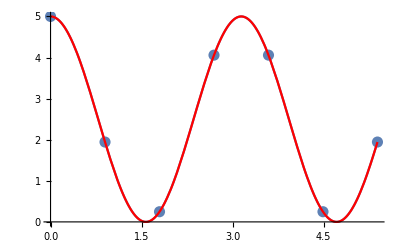

```mathematica
f[x_]=5(Cos[x])^2;
NN=7;
X=Table[Subscript[x, k]=(2Pi*k)/NN,{k,0,NN-1}];
F=f[X];
Subscript[f, k_]:=F[[k+1]];
n=(NN-1)/2;
Do[Subscript[C, k]=1/NN∑_(j=0)^(NN-1) Subscript[f, j]*Exp[I*(2Pi)/NN]^(-k*j),{k,-n,n}];
T[x_]=∑_(k=-n)^n Subscript[C, k]*Exp[I*x]^k//FullSimplify
Table[(T[Subscript[x, j]]//N)==(Subscript[f, j]//N),{j,0,NN-1}]
Gr1=ListPlot[MapThread[List,{X,F}],PlotStyle->{PointSize[0.02]}];
Gr2=Plot[f[y],{y,Subscript[x, 0],Subscript[x, NN-1]}];
Gr3=Plot[T[y],{y,Subscript[x, 0],Subscript[x, NN-1]},PlotStyle->Red];
Show[Gr1,Gr2,Gr3,PlotRange->All]
```

Задание 3

```mathematica
XX={1/10,2/10,3/10,4/10};
f={1.87,2.054,5.909,8.872};
n=Length[XX]-1;Subscript[xx, k_]:=XX[[k+1]];Subscript[f, k_]:=f[[k+1]]
eqv[m_,y_]:=Table[(D[x^i,{x,m}]//.x->y)==∑_(k=0)^n Subscript[d, k]*Subscript[xx, k]^i,{i,0,n}]
Pr[m_,y_]:=∑_(k=0)^n Subscript[d, k]*Subscript[f, k]//.(Solve[eqv[m,y],{}]//Flatten)
{Pr[1,1/10],Pr[1,2/10],Pr[2,0],Pr[3,5/10]}
```

{-31.725,27.8,1279.7,-4563.}

```mathematica
P[x_]=InterpolatingPolynomial[Table[{Subscript[xx, k],Subscript[f, k]},{k,0,n}],x];
Pr1[m_,y_]:=D[P[x],{x,m}]//.x->y
{Pr1[1,1/10]==Pr[1,1/10],Pr1[1,2/10]==Pr[1,2/10],Pr1[2,0]==Pr[2,0],Pr1[3,5/10]==Pr[3,5/10]}
```

{True,True,True,True}

```mathematica
Pogr[m_,y_]:=M/((n+1)!)Abs[D[∏_(k=0)^n (x-Subscript[xx, k]),{x,m}]//.x->y]
{Pogr[1,1/10],Pogr[1,2/10],Pogr[2,0],Pogr[3,5/10]}
```

{M/4000,M/12000,(7 M)/240,M/4}

```mathematica
Table[M/((n+1)!)Maximize[{Abs[D[∏_(k=0)^n (x-Subscript[xx, k]),{x,m}]],0≤x≤5/10},x][[1]],{m,0,n+2}]
```

{M/10000,M/480,(7 M)/240,M/4,M,0}